# c.quark-flow.decompose.normal.ed6.nb

```mathematica
NotebookFileName[]
```

C:\Users\Tom\Desktop\octet.sea-valence\c.quark-flow.decompose.normal.nb

```mathematica
Quit[]
```

pre run by order:

Gen.Vertex.Dict.constituent.all

c.quark-flow.coe.nb

## note

## c.quark-flow.decompose.normal.ed3.nb

只有qfa quarkflow 图的chpt图 是没有冗余性的，不能随意指定对称性，

而同时有qfa和qfb的图就可以在qfa中 随意指定对称性，因为由此带来的负作用被qfb吃掉了。所以，对于不同的八重态的Σ-Λ图，需要指定不同的benchmark。

每个系列是同样的道理

solve the Σ-Λ u d s sea loop don’t equal question

the key quarkflow names will be the  “loop quarkflow names”, i.e. in position “p2“ or ”p3”

to pickup a specify diagram, only need the meson names. cause the mediate baryons can change, but the mesons will be the same.

********************************************************************

这次的顶点应该考虑某一个味道的贡献时，不用乘以 1/2，因为解方程时，自然考虑了这个因素，比如 "p4", "p5" 的同样夸克，味道是相同的，

这个在 typea`external`equation 考虑了进去。

## this time 7 kinds

a  d e f g, 1, 4, 5;

b, 2; consider the  EM vertexes in here

c, 3; consider the  EM vertexes in here

h m n o p, 6, 10, 11;

i 7

j 8

k l, 9

## note: how to decompose

Note  the difference between determining (di,fi) and

reaction channel

type

## initial

fucoeandmrrlabbr

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"/expression-coes/"}]]
```

C:\Users\Tom\Desktop\octet.sea-valence\expression-coes

```mathematica
name`fucoeandmrrlabbr`string`normal=FileNameJoin[{Directory[],"fucoeandmrrlabbr.string.normal.m"}];
Once[fucoeandmrrlabbr`string`normal=Get[name`fucoeandmrrlabbr`string`normal]];
```

```mathematica
name`fucoeandmrrlabbr`normal=FileNameJoin[{Directory[],"fucoeandmrrlabbr.normal.m"}];
Once[fucoeandmrrlabbr`normal=Get[name`fucoeandmrrlabbr`normal]];
```

```mathematica
(*name`fucoeandmrrlabbr`symmetry=FileNameJoin[{Directory[],"fucoeandmrrlabbr.symmetry.m"}];
Once[fucoeandmrrlabbr`symmetry=Get[name`fucoeandmrrlabbr`symmetry]];*)
```

odm name by mass list

onbml = {"Σm", "Σ0", "Σp", "Np", "Nn", "Ξm", "Ξ0", "Λ"};

mnbml={"πim","πi0","πip","Κi0","OverBar[Κi0]","Κim","Κip","η"};

dnbml = {"Δm", "Δ0", "Δp", "Δpp", "Σsm", "Σs0", "Σsp", "Ξsm", "Ξs0", "Ωm"};

quark model representation

give the quark model presentation of mesons, baryons,

```mathematica
octetquarktypea=<|
"s,d,d,1"->"Σm",
"d,s,d,1"->"Σm",

"u,d,s,1"->"Σ0",
"d,u,s,1"->"Σ0",
"s,d,u,1"->"Σ0",

"u,u,s,1"->"Σp",
"s,u,u,1"->"Σp",

"u,d,u,1"->"Np",
"d,u,u,1"->"Np",

"u,d,d,1"->"Nn",
"d,d,u,1"->"Nn",

"d,s,s,1"->"Ξm",
"s,s,d,1"->"Ξm",

"u,s,s,1"->"Ξ0",
"s,u,s,1"->"Ξ0",

"u,d,s,2"->"Λ",
"d,u,s,2"->"Λ",
"s,d,u,2"->"Λ",

"u,u,u,1"->"uuu",
"d,d,d,1"->"ddd",
"s,s,s,1"->"sss"
|>;
```

```mathematica
octetquarktypeb=<|
"s,d,d,1"->"Σm",
"d,s,d,1"->"Σm",
"d,d,s,1"->"Σm",

"u,d,s,1"->"Σ0",
"d,u,s,1"->"Σ0",
"s,d,u,1"->"Σ0",
"d,s,u,1"->"Σ0",
"s,u,d,1"->"Σ0",
"u,s,d,1"->"Σ0",

"u,u,s,1"->"Σp",
"s,u,u,1"->"Σp",
"u,s,u,1"->"Σp",

"u,u,d,1"->"Np",
"u,d,u,1"->"Np",
"d,u,u,1"->"Np",

"u,d,d,1"->"Nn",
"d,d,u,1"->"Nn",
"d,u,d,1"->"Nn",

"d,s,s,1"->"Ξm",
"s,s,d,1"->"Ξm",
"s,d,s,1"->"Ξm",

"u,s,s,1"->"Ξ0",
"s,u,s,1"->"Ξ0",
"s,s,u,1"->"Ξ0",

"u,d,s,2"->"Λ",
"d,u,s,2"->"Λ",
"s,d,u,2"->"Λ",
"d,s,u,2"->"Λ",
"s,u,d,2"->"Λ",
"u,s,d,2"->"Λ",

"u,u,u,1"->"uuu",
"d,d,d,1"->"ddd",
"s,s,s,1"->"sss"
|>;
```

```mathematica
mesonquark=<|
"u,u,1"->"η",
"d,d,1"->"η",
"s,s,1"->"η",

"u,u,3"->"etas",(*add η singlet*)
"d,d,3"->"etas",
"s,s,3"->"etas",

"u,u,2"->"πi0",
"d,d,2"->"πi0",

"u,d,1"->"πip",

"d,u,1"->"πim",

"u,s,1"->"Κip",
"s,u,1"->"Κim",

"d,s,1"->"Κi0",
"s,d,1"->"Κi0b"
|>;
```

```mathematica
mesonquark`mag=<|(*special made for calc of magnetic figures 2 3 9 to solve πi0-η problem, but in this version, maybe not needed anymore.*)
"u,u,1"->"η",
"d,d,1"->"η",
"s,s,1"->"η",

"u,u,3"->"etas",(*add η singlet*)
"d,d,3"->"etas",
"s,s,3"->"etas",

"u,u,2"->"πi0",
"d,d,2"->"πi0",
(*"s,sbar,2"->"πi0", *) (*in this version, maybe not needed anymore*)

"u,d,1"->"πip",

"d,u,1"->"πim",

"u,s,1"->"Κip",
"s,u,1"->"Κim",

"d,s,1"->"Κi0",
"s,d,1"->"Κi0b"

|>;
```

```mathematica
decupletquarktypea=<|
"d,d,d,1"->"Δm",

"u,d,d,1"->"Δ0",
"d,u,d,1"->"Δ0",

"u,d,u,1"->"Δp",
"d,u,u,1"->"Δp",

"u,u,u,1"->"Δpp",

"s,d,d,1"->"Σsm",
"d,s,d,1"->"Σsm",

"s,u,d,1"->"Σs0",
"d,s,u,1"->"Σs0",
"u,d,s,1"->"Σs0",

"s,u,u,1"->"Σsp",
"u,s,u,1"->"Σsp",

"d,s,s,1"->"Ξsm",
"s,d,s,1"->"Ξsm",

"u,s,s,1"->"Ξs0",
"s,u,s,1"->"Ξs0",
 
"s,s,s,1"->"Ωm"
|>;
```

```mathematica
decupletquarktypeb=<|
"d,d,d,1"->"Δm",

"u,d,d,1"->"Δ0",
"d,u,d,1"->"Δ0",
"d,d,u,1"->"Δ0",

"u,u,d,1"->"Δp",
"u,d,u,1"->"Δp",
"d,u,u,1"->"Δp",

"u,u,u,1"->"Δpp",

"s,d,d,1"->"Σsm",
"d,s,d,1"->"Σsm",
"d,d,s,1"->"Σsm",

"s,u,d,1"->"Σs0",
"d,s,u,1"->"Σs0",
"u,d,s,1"->"Σs0",
"s,d,u,1"->"Σs0",
"d,u,s,1"->"Σs0",
"u,s,d,1"->"Σs0",

"s,u,u,1"->"Σsp",
"u,s,u,1"->"Σsp",
"u,u,s,1"->"Σsp",

"d,s,s,1"->"Ξsm",
"s,d,s,1"->"Ξsm",
"s,s,d,1"->"Ξsm",

"u,s,s,1"->"Ξs0",
"s,u,s,1"->"Ξs0",
"s,s,u,1"->"Ξs0",
 
"s,s,s,1"->"Ωm"
|>;
```

## quark flow for calc

in this edition, not the previous name form “q2`f5`o1`qfa`sdd`sdbar`Κi0b”

but the new quark`flow name form “s`f5`o1`qfa`sdd`sdbar`Κi0b`p1”

“s” is the photon bond quark name, while “p1” is abbreviation of  the “position 1“, “p1,p2,p3,p4,p5”, total 5 position in the middle of the diagrams

type A

sea diagram

mesonquark,octetquarktypeb,decupletquarktypeb

the new quark`flow name form "s`f5`o1`qfa`sdd`sdbar`Κi0b`p1"

## cal`typea1 (1 4 5)

typea chosen ones: a1, a2, a3, b3

a1=a1,  a2=a2,  a3=a3, 
 b1=a1, b2=b3, b3=b3, b4=a2, b5=a3,

```mathematica
cal`typea1[position_,pname_]:=Block[{teorder,tenm},
(*for example [1,"p1"]*)
Table[(*diagram 1 4 5*)
DeleteMissing[
Flatten[
Table[(*table of quark flow*)
{
(teorder=({a1,b3}⟦position⟧)<>"`f1`o"<>ToString[io])<>
"`"<>"qfa`"<>a1<>a2<>a3<>"`"<>a1<>b3
<>"`"<>(mesonquark⟦a1<>","<>b3<>","<>num3⟧/._Missing->Sequence[])
<>"`"<>pname(* position 1*),

teorder<>(tenm="`"<>
(octetquarktypea⟦a1<>","<>a2<>","<>a3<>","<>num1⟧/._Missing->Sequence[])<>"`"<>
(octetquarktypeb⟦b3<>","<>a2<>","<>a3<>","<>num2⟧/._Missing->Sequence[])<>"`"<>
(mesonquark⟦a1<>","<>b3<>","<>num3⟧/._Missing->Sequence[])
)
}
->
Part[
Association[
fucoeandmrrlabbr`string`normal⟦1,io⟧
],(* part parameter 1 *)
teorder<>tenm
]
,{a1,{"u","d","s"}}
,{a2,{"u","d","s"}}
,{a3,{"u","d","s"}}
,{b3,{"u","d","s"}}
,{num1,{"1","2","3"}}
,{num2,{"1","2","3"}}
,{num3,{"1","2","3"}}
]
]
]
,{io,1,8,1}
]
]
```

## typea2 ( 2 )

typea chosen ones: a1, a2, a3, b3

a1=a1,  a2=a2,  a3=a3, 
 b1=a1, b2=b3, b3=b3, b4=a2, b5=a3,

```mathematica
cal`typea2[position_,pname_]:=Block[{teorder,tenm},(*for example [1,"p1"]*)
Table[(*diagram 2*)
DeleteMissing[
Flatten[
Table[
{
(teorder=({b3,a2,a3}⟦position⟧)<>"`f2`o"<>ToString[io])<>
"`"<>"qfa`"<>a1<>a2<>a3<>"`"<>a1<>b3
<>"`"<>(mesonquark`mag⟦a1<>","<>b3<>","<>num4⟧/._Missing->Sequence[])
<>"`"<>pname,(* position 1*)

teorder<>(tenm="`"<>
(octetquarktypea⟦a1<>","<>a2<>","<>a3<>","<>num1⟧/._Missing->Sequence[])<>"`"<>
(octetquarktypeb⟦b3<>","<>a2<>","<>a3<>","<>num2⟧/._Missing->Sequence[])<>"`"<>
(octetquarktypeb⟦b3<>","<>a2<>","<>a3<>","<>num3⟧/._Missing->Sequence[])<>"`"<>
(mesonquark`mag⟦a1<>","<>b3<>","<>num4⟧/._Missing->Sequence[])
)
}
->
Part[
Association[
fucoeandmrrlabbr`string`normal⟦2,io⟧
],(* part parameter 1 *)
teorder<>tenm
]
,{a1,{"u","d","s"}}
,{a2,{"u","d","s"}}
,{a3,{"u","d","s"}}
,{b3,{"u","d","s"}}
,{num1,{"1","2","3"}}
,{num2,{"1","2","3"}}
,{num3,{"1","2","3"}}
,{num4,{"1","2","3"}}
]
]
]
,{io,1,8,1}
]
];
```

## typea3 (3 )

```mathematica
cal`typea3[position_,pname_]:=Block[{teorder,tenm},(*for example [1,"p1"]*)
Table[(*diagram 3*)
DeleteMissing[
Flatten[
Table[
{
(teorder=({b3,a2,a3}⟦position⟧)<>"`f3`o"<>ToString[io])<>
"`"<>"qfa`"<>a1<>a2<>a3<>"`"<>a1<>b3
<>"`"<>(mesonquark`mag⟦a1<>","<>b3<>","<>num4⟧/._Missing->Sequence[])
<>"`"<>pname(* position 1*),

teorder<>(tenm="`"<>
(octetquarktypea⟦a1<>","<>a2<>","<>a3<>","<>num1⟧/._Missing->Sequence[])<>"`"<>
(octetquarktypeb⟦b3<>","<>a2<>","<>a3<>","<>num2⟧/._Missing->Sequence[])<>"`"<>
(octetquarktypeb⟦b3<>","<>a2<>","<>a3<>","<>num3⟧/._Missing->Sequence[])<>"`"<>
(mesonquark`mag⟦a1<>","<>b3<>","<>num4⟧/._Missing->Sequence[])
)
}
->
Part[
Association[
fucoeandmrrlabbr`string`normal⟦3,io⟧
],(* part parameter 1 *)
teorder<>tenm
]
,{a1,{"u","d","s"}}
,{a2,{"u","d","s"}}
,{a3,{"u","d","s"}}
,{b3,{"u","d","s"}}
,{num1,{"1","2","3"}}
,{num2,{"1","2","3"}}
,{num3,{"1","2","3"}}
,{num4,{"1","2","3"}}
]
]
]
,{io,1,8,1}
]
];
```

## typea4 (6 10 11)

```mathematica
cal`typea4[position_,pname_]:=Block[{teorder,tenm},(*for example [1,"p1"]*)
Table[(*diagram 6 10 11*)
DeleteMissing[
Flatten[
Table[
{
(teorder=({a1,b3}⟦position⟧)<>"`f4`o"<>ToString[io])<>
"`"<>"qfa`"<>a1<>a2<>a3<>"`"<>a1<>b3
<>"`"<>(mesonquark⟦a1<>","<>b3<>","<>num2⟧/._Missing->Sequence[])
<>"`"<>pname(* position 1*),

teorder<>(tenm="`"<>
(octetquarktypea⟦a1<>","<>a2<>","<>a3<>","<>num1⟧/._Missing->Sequence[])<>"`"<>
(decupletquarktypeb⟦b3<>","<>a2<>","<>a3<>","<>"1"⟧/._Missing->Sequence[])<>"`"<>
(mesonquark⟦a1<>","<>b3<>","<>num2⟧/._Missing->Sequence[])
)
} 
->
Part[
Association[
fucoeandmrrlabbr`string`normal⟦4,io⟧
],(*part parameter 1*)
teorder<>tenm
]
,{a1,{"u","d","s"}}
,{a2,{"u","d","s"}}
,{a3,{"u","d","s"}}
,{b3,{"u","d","s"}}
,{num1,{"1","2","3"}}
,{num2,{"1","2","3"}}
]
]
]
,{io,1,8,1}
]
];
```

## typea5 (7)

```mathematica
cal`typea5[position_,pname_]:=Block[{teorder,tenm},(*for example [1,"p1"]*)
Table[(*diagram 7 8*)
DeleteMissing[
Flatten[
Table[
{
(teorder=({b3,a2,a3}⟦position⟧)<>"`f5`o"<>ToString[io])<>
"`"<>"qfa`"<>a1<>a2<>a3<>"`"<>a1<>b3
<>"`"<>(mesonquark⟦a1<>","<>b3<>","<>num2⟧/._Missing->Sequence[])
<>"`"<>pname(* position 1*),

teorder<>(tenm="`"<>
(octetquarktypea⟦a1<>","<>a2<>","<>a3<>","<>num1⟧/._Missing->Sequence[])<>"`"<>
(decupletquarktypeb⟦b3<>","<>a2<>","<>a3<>","<>"1"⟧/._Missing->Sequence[])<>"`"<>
(mesonquark⟦a1<>","<>b3<>","<>num2⟧/._Missing->Sequence[])
)
} 
->
Part[
Association[
fucoeandmrrlabbr`string`normal⟦5,io⟧
],(*part parameter 1*)
teorder<>tenm
]
,{a1,{"u","d","s"}}
,{a2,{"u","d","s"}}
,{a3,{"u","d","s"}}
,{b3,{"u","d","s"}}
,{num1,{"1","2","3"}}
,{num2,{"1","2","3"}}
]
]
]
,{io,1,8,1}
]
];
```

## typea6 (8)

```mathematica
cal`typea6[position_,pname_]:=Block[{teorder,tenm},(*for example [1,"p1"]*)
Table[(*diagram 7 8*)
DeleteMissing[
Flatten[
Table[
{
(teorder=({b3,a2,a3}⟦position⟧)<>"`f6`o"<>ToString[io])<>
"`"<>"qfa`"<>a1<>a2<>a3<>"`"<>a1<>b3
<>"`"<>(mesonquark⟦a1<>","<>b3<>","<>num2⟧/._Missing->Sequence[])
<>"`"<>pname(* position 1*),

teorder<>(tenm="`"<>
(octetquarktypea⟦a1<>","<>a2<>","<>a3<>","<>num1⟧/._Missing->Sequence[])<>"`"<>
(decupletquarktypeb⟦b3<>","<>a2<>","<>a3<>","<>"1"⟧/._Missing->Sequence[])<>"`"<>
(mesonquark⟦a1<>","<>b3<>","<>num2⟧/._Missing->Sequence[])
)
} 
->
Part[
Association[
fucoeandmrrlabbr`string`normal⟦6,io⟧
],(*part parameter 1*)
teorder<>tenm
]
,{a1,{"u","d","s"}}
,{a2,{"u","d","s"}}
,{a3,{"u","d","s"}}
,{b3,{"u","d","s"}}
,{num1,{"1","2","3"}}
,{num2,{"1","2","3"}}
]
]
]
,{io,1,8,1}
]
];
```

## typea7 (9)

```mathematica
cal`typea7[position_,pname_]:=Block[{teorder,tenm},(*for example [1,"p1"]*)
Table[(*diagram 9*)
DeleteMissing[
Flatten[
Table[
{
(teorder=({b3,a2,a3}⟦position⟧)<>"`f7`o"<>ToString[io])<>
"`"<>"qfa`"<>a1<>a2<>a3<>"`"<>a1<>b3
<>"`"<>(mesonquark`mag⟦a1<>","<>b3<>","<>num3⟧/._Missing->Sequence[])
<>"`"<>pname(* position 1*),

teorder<>(tenm="`"<>
(octetquarktypea⟦a1<>","<>a2<>","<>a3<>","<>num1⟧/._Missing->Sequence[])<>"`"<>
(decupletquarktypeb⟦b3<>","<>a2<>","<>a3<>","<>"1"⟧/._Missing->Sequence[])<>"`"<>
(octetquarktypeb⟦b3<>","<>a2<>","<>a3<>","<>num2⟧/._Missing->Sequence[])<>"`"<>
(mesonquark`mag⟦a1<>","<>b3<>","<>num3⟧/._Missing->Sequence[])
)
} 
->
Part[
Association[
fucoeandmrrlabbr`string`normal⟦7,io⟧
],(*part parameter 1*)
teorder<>tenm
]
,{a1,{"u","d","s"}}
,{a2,{"u","d","s"}}
,{a3,{"u","d","s"}}
,{b3,{"u","d","s"}}
,{num1,{"1","2","3"}}
,{num2,{"1","2","3"}}
,{num3,{"1","2","3"}}
]
]
]
,{io,1,8,1}
]
];
```

type B

quench diagram

mesonquark,octetquarktypeb,decupletquarktypeb

the new quark`flow name form "s`f5`o1`qfa`sdd`sdbar`Κi0b`p1"

type b has no repetition, no identical lines in a1 a2 a3

## typeb1 ( 1 4 5)

typea chosen ones: a1, a2, a3

a1=a1,  a2=a2,  a3=a3, 
 b1=a1, b2=a2, b3=a2, b4=a2, b5=a3,

```mathematica
cal`typeb1[position_,pname_]:=Block[{teorder,tenm},(*for example [1,"p1"]*)
Table[(*diagram 1 4 5*)
DeleteMissing[
Flatten[
Table[
{
(teorder=({a1,a2}⟦position⟧)<>"`f1`o"<>ToString[io])<>
"`"<>"qfb`"<>a1<>a2<>a3<>"`"<>a1<>a2
<>"`"<>(mesonquark⟦a1<>","<>a2<>","<>num3⟧/._Missing->Sequence[])
<>"`"<>pname(* position 1*),

teorder<>(tenm="`"<>
(octetquarktypeb⟦a1<>","<>a2<>","<>a3<>","<>num1⟧/._Missing->Sequence[])<>"`"<>
(octetquarktypeb⟦a2<>","<>a2<>","<>a3<>","<>num2⟧/._Missing->Sequence[])<>"`"<>
(mesonquark⟦a1<>","<>a2<>","<>num3⟧/._Missing->Sequence[])
)
} 
->
Part[
Association[
fucoeandmrrlabbr`string`normal⟦1,io⟧
],(*part parameter 1*)
teorder<>tenm
]
,{a1,{"u","d","s"}}
,{a2,{"u","d","s"}}
,{a3,{"u","d","s"}}
,{num1,{"1","2","3"}}
,{num2,{"1","2","3"}}
,{num3,{"1","2","3"}}
]
]
]
,{io,1,8,1}
]
];
```

## typeb2 (2) special

```mathematica
cal`typeb2[position_,pname_]:=Block[{teorder,tenm},
Table[
DeleteMissing[
Flatten[
Table[
{
(teorder=({a2,a2,a3}⟦position⟧)<>"`f2`o"<>ToString[io])<>
"`"<>"qfb`"<>a1<>a2<>a3<>"`"<>a1<>a2
<>"`"<>(mesonquark`mag⟦a1<>","<>a2<>","<>num4⟧/._Missing->Sequence[])
<>"`"<>pname(* position 1*),

teorder<>(tenm="`"<>
(octetquarktypeb⟦a1<>","<>a2<>","<>a3<>","<>num1⟧/._Missing->Sequence[])<>"`"<>
(octetquarktypeb⟦a2<>","<>a2<>","<>a3<>","<>num2⟧/._Missing->Sequence[])<>"`"<>
(octetquarktypeb⟦a2<>","<>a2<>","<>a3<>","<>num3⟧/._Missing->Sequence[])<>"`"<>
(mesonquark`mag⟦a1<>","<>a2<>","<>num4⟧/._Missing->Sequence[])
)
} 
->
Part[
Association[
fucoeandmrrlabbr`string`normal⟦2,io⟧
],(*part parameter 1*)
teorder<>tenm
]
,{a1,{"u","d","s"}}
,{a2,{"u","d","s"}}
,{a3,{"u","d","s"}}
,{num1,{"1","2","3"}}
,{num2,{"1","2","3"}}
,{num3,{"1","2","3"}}
,{num4,{"1","2","3"}}
]
]
]
,{io,1,8,1}
]
];
```

## typeb3 (3) special

```mathematica
cal`typeb3[position_,pname_]:=Block[{teorder,tenm},
Table[
DeleteMissing[
Flatten[
Table[
{
(teorder=({a2,a2,a3}⟦position⟧)<>"`f3`o"<>ToString[io])<>
"`"<>"qfb`"<>a1<>a2<>a3<>"`"<>a1<>a2
<>"`"<>(mesonquark`mag⟦a1<>","<>a2<>","<>num4⟧/._Missing->Sequence[])
<>"`"<>pname(* position 1*),

teorder<>(tenm="`"<>
(octetquarktypeb⟦a1<>","<>a2<>","<>a3<>","<>num1⟧/._Missing->Sequence[])<>"`"<>
(octetquarktypeb⟦a2<>","<>a2<>","<>a3<>","<>num2⟧/._Missing->Sequence[])<>"`"<>
(octetquarktypeb⟦a2<>","<>a2<>","<>a3<>","<>num3⟧/._Missing->Sequence[])<>"`"<>
(mesonquark`mag⟦a1<>","<>a2<>","<>num4⟧/._Missing->Sequence[])
)
} 
->
Part[
Association[
fucoeandmrrlabbr`string`normal⟦3,io⟧
],(*part parameter 1*)
teorder<>tenm
]
,{a1,{"u","d","s"}}
,{a2,{"u","d","s"}}
,{a3,{"u","d","s"}}
,{num1,{"1","2","3"}}
,{num2,{"1","2","3"}}
,{num3,{"1","2","3"}}
,{num4,{"1","2","3"}}
]
]
]
,{io,1,8,1}
]
];
```

## typea4 (6 10 11)

```mathematica
cal`typeb4[position_,pname_]:=Block[{teorder,tenm},
Table[
DeleteMissing[
Flatten[
Table[
{
(teorder=({a1,a2}⟦position⟧)<>"`f4`o"<>ToString[io])<>
"`"<>"qfb`"<>a1<>a2<>a3<>"`"<>a1<>a2
<>"`"<>(mesonquark⟦a1<>","<>a2<>","<>num2⟧/._Missing->Sequence[])
<>"`"<>pname(* position 1*),

teorder<>(tenm="`"<>
(octetquarktypeb⟦a1<>","<>a2<>","<>a3<>","<>num1⟧/._Missing->Sequence[])<>"`"<>
(decupletquarktypeb⟦a2<>","<>a2<>","<>a3<>","<>"1"⟧/._Missing->Sequence[])<>"`"<>
(mesonquark⟦a1<>","<>a2<>","<>num2⟧/._Missing->Sequence[])
)
} 
->
Part[
Association[
fucoeandmrrlabbr`string`normal⟦4,io⟧
],(*part parameter 1*)
teorder<>tenm
]
,{a1,{"u","d","s"}}
,{a2,{"u","d","s"}}
,{a3,{"u","d","s"}}
,{num1,{"1","2","3"}}
,{num2,{"1","2","3"}}
]
]
]
,{io,1,8,1}
]
];
```

## typea5 (7)

```mathematica
cal`typeb5[position_,pname_]:=Block[{teorder,tenm},
Table[
DeleteMissing[
Flatten[
Table[
{
(teorder=({a2,a2,a3}⟦position⟧)<>"`f5`o"<>ToString[io])<>
"`"<>"qfb`"<>a1<>a2<>a3<>"`"<>a1<>a2
<>"`"<>(mesonquark⟦a1<>","<>a2<>","<>num2⟧/._Missing->Sequence[])
<>"`"<>pname(* position 1*),

teorder<>(tenm="`"<>
(octetquarktypeb⟦a1<>","<>a2<>","<>a3<>","<>num1⟧/._Missing->Sequence[])<>"`"<>
(decupletquarktypeb⟦a2<>","<>a2<>","<>a3<>","<>"1"⟧/._Missing->Sequence[])<>"`"<>
(mesonquark⟦a1<>","<>a2<>","<>num2⟧/._Missing->Sequence[])
)
} 
->
Part[
Association[
fucoeandmrrlabbr`string`normal⟦5,io⟧
],(*part parameter 1*)
teorder<>tenm
]
,{a1,{"u","d","s"}}
,{a2,{"u","d","s"}}
,{a3,{"u","d","s"}}
,{num1,{"1","2","3"}}
,{num2,{"1","2","3"}}
]
]
]
,{io,1,8,1}
]
];
```

## typea6 (8)

```mathematica
cal`typeb6[position_,pname_]:=Block[{teorder,tenm},
Table[
DeleteMissing[
Flatten[
Table[
{
(teorder=({a2,a2,a3}⟦position⟧)<>"`f6`o"<>ToString[io])<>
"`"<>"qfb`"<>a1<>a2<>a3<>"`"<>a1<>a2
<>"`"<>(mesonquark⟦a1<>","<>a2<>","<>num2⟧/._Missing->Sequence[])
<>"`"<>pname(* position 1*),

teorder<>(tenm="`"<>
(octetquarktypeb⟦a1<>","<>a2<>","<>a3<>","<>num1⟧/._Missing->Sequence[])<>"`"<>
(decupletquarktypeb⟦a2<>","<>a2<>","<>a3<>","<>"1"⟧/._Missing->Sequence[])<>"`"<>
(mesonquark⟦a1<>","<>a2<>","<>num2⟧/._Missing->Sequence[])
)
} 
->
Part[
Association[
fucoeandmrrlabbr`string`normal⟦6,io⟧
],(*part parameter 1*)
teorder<>tenm
]
,{a1,{"u","d","s"}}
,{a2,{"u","d","s"}}
,{a3,{"u","d","s"}}
,{num1,{"1","2","3"}}
,{num2,{"1","2","3"}}
]
]
]
,{io,1,8,1}
]
];
```

## typeb7 (9)special

```mathematica
cal`typeb7[position_,pname_]:=Block[{teorder,tenm},
Table[
DeleteMissing[
Flatten[
Table[
{
(teorder=({a2,a2,a3}⟦position⟧)<>"`f7`o"<>ToString[io])<>
"`"<>"qfb`"<>a1<>a2<>a3<>"`"<>a1<>a2
<>"`"<>(mesonquark`mag⟦a1<>","<>a2<>","<>num3⟧/._Missing->Sequence[])
<>"`"<>pname(* position 1*),

teorder<>(tenm="`"<>
(octetquarktypeb⟦a1<>","<>a2<>","<>a3<>","<>num1⟧/._Missing->Sequence[])<>"`"<>
(decupletquarktypeb⟦a2<>","<>a2<>","<>a3<>","<>"1"⟧/._Missing->Sequence[])<>"`"<>
(octetquarktypeb⟦a2<>","<>a2<>","<>a3<>","<>num2⟧/._Missing->Sequence[])<>"`"<>
(mesonquark`mag⟦a1<>","<>a2<>","<>num3⟧/._Missing->Sequence[])
)
} 
->
Part[
Association[
fucoeandmrrlabbr`string`normal⟦7,io⟧
],(*part parameter 1*)
teorder<>tenm
]
,{a1,{"u","d","s"}}
,{a2,{"u","d","s"}}
,{a3,{"u","d","s"}}
,{num1,{"1","2","3"}}
,{num2,{"1","2","3"}}
,{num3,{"1","2","3"}}
]
]
]
,{io,1,8,1}
]
];
```

join into typea & typeb

```mathematica
cal`typea={
Join[cal`typea1[1,"p1"],cal`typea1[2,"p2"],2],(*1,4,5,join only at the secound level*)

Join[cal`typea2[1,"p3"],cal`typea2[2,"p4"],cal`typea2[3,"p5"],2],(*2*)

Join[cal`typea3[1,"p3"],cal`typea3[2,"p4"],cal`typea3[3,"p5"],2],(*3*)

Join[cal`typea4[1,"p1"],cal`typea4[2,"p2"],2],(*6,10,11*)

Join[cal`typea5[1,"p3"],cal`typea5[2,"p4"],cal`typea5[3,"p5"],2],(*7*)

Join[cal`typea6[1,"p3"],cal`typea6[2,"p4"],cal`typea6[3,"p5"],2],(*8*)

Join[cal`typea7[1,"p3"],cal`typea7[2,"p4"],cal`typea7[3,"p5"],2](*9*)
};
```

```mathematica
cal`typeb={
Join[cal`typeb1[1,"p1"],cal`typeb1[2,"p2"],2],(*1,4,5*)

Join[cal`typeb2[1,"p3"],cal`typeb2[2,"p4"],cal`typeb2[3,"p5"],2],(*2*)

Join[cal`typeb3[1,"p3"],cal`typeb3[2,"p4"],cal`typeb3[3,"p5"],2],(*3*)

Join[cal`typeb4[1,"p1"],cal`typeb4[2,"p2"],2],(*6,10,11*)

Join[cal`typeb5[1,"p3"],cal`typeb5[2,"p4"],cal`typeb5[3,"p5"],2],(*7*)

Join[cal`typeb6[1,"p3"],cal`typeb6[2,"p4"],cal`typeb6[3,"p5"],2],(*8*)

Join[cal`typeb7[1,"p3"],cal`typeb7[2,"p4"],cal`typeb7[3,"p5"],2](*9*)
};
```

```mathematica
cal`typea//Dimensions
cal`typeb//Dimensions
```

## chpt quarkflow equations

chqftransfer1 chpt → quark flow

gives the reflection: chpt diagrams → quark flow diagrams

```mathematica
chqftransfer1=Table[
Merge[
Join[
MapThread[Rule,(*typea*)
{
Map[Symbol,Keys[cal`typea⟦if,io⟧]⟦;;,2⟧],(*chpt name/feynman basis*)
Map[Symbol,Keys[cal`typea⟦if,io⟧]⟦;;,1⟧](*quark flow basis*)
}
],
MapThread[Rule,(*typeb*)
{
Map[Symbol,Keys[cal`typeb⟦if,io⟧]⟦;;,2⟧],(*chpt name/feynman basis*)
Map[Symbol,Keys[cal`typeb⟦if,io⟧]⟦;;,1⟧](*quark flow basis*)
}
]
],
Total
]
,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
```

```mathematica
chqftransfer1//Dimensions
```

chqftransfer2 quark`flow → chpt

gives the reflection: quark`flow diagrams → chpt diagrams

```mathematica
chqftransfer2=Table[
Merge[
Join[
MapThread[Rule,(*typea*)
{
Map[Symbol,Keys[cal`typea⟦if,io⟧]⟦;;,1⟧],(*quark flow basis*)
Map[Symbol,Keys[cal`typea⟦if,io⟧]⟦;;,2⟧](*chpt name/feynman basis*)
}
],
MapThread[Rule,(*typeb*)
{
Map[Symbol,Keys[cal`typeb⟦if,io⟧]⟦;;,1⟧],(*quark flow basis*)
Map[Symbol,Keys[cal`typeb⟦if,io⟧]⟦;;,2⟧](*chpt name/feynman basis*)
}
]
],
Total
]
,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
```

```mathematica
chqftransfer2//Dimensions
```

quarkflow`names

```mathematica
quarkflow`names=Table[
DeleteDuplicates[
Keys[Normal[chqftransfer2⟦if,io⟧]]
]
,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
```

```mathematica
chpt`names=Table[
DeleteDuplicates[
Keys[Normal[chqftransfer1⟦if,io⟧]]
]
,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
```

## chptquark`transfereq

gives the equation to determining the [di,fi] of quark`flow  diagrams, a two-way reflection (bijection)

chqftransfer1 chpt[key]→ quark flow[value]

chqftransfer2 quark`flow[key]→ chpt[value]

```mathematica
chptquark`transfereq=Table[
DeleteDuplicates[
MapThread[Equal,
{
(*chpt diagrams*)
(
Values[chqftransfer1⟦if,io⟧](*quark flow basis*)
/.Normal[chqftransfer2⟦if,io⟧](*to chpt basis*)
/.Normal[chqftransfer1⟦if,io⟧](*to quark flow basis*)
/.Normal[chqftransfer2⟦if,io⟧](*to chpt basis*)
)/._Integer->1/._Integer->1/._Integer->1/._Integer->1,
(*chpt diagrams*)

(*quark flow diagrams*)
(
Values[chqftransfer1⟦if,io⟧](*quark flow*)
/.Normal[chqftransfer2⟦if,io⟧](*chpt flow*)
/.Normal[chqftransfer1⟦if,io⟧](*quark flow*)
/.Normal[chqftransfer2⟦if,io⟧](*chpt flow*)
/.Normal[chqftransfer1⟦if,io⟧](*quark flow*)
)/._Integer->1/._Integer->1/._Integer->1/._Integer->1
(*chpt diagrams*)
(*quark flow diagrams*)
}
]
]
,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
```

```mathematica
chptquark`transfereq//Dimensions
```

## typea equivalence equation

Only both position and valence environment are the same, the  amplitude is  claimed to be identity.

but for io=2 and 8, Σ0 and Λ, the type`b external equation is enough to determine all key value in each series, so delete equation have random two of  π0 η and etas,

typea`series

```mathematica
typea`series=Table[
{}
,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
```

d`f1`o1`qfb`dds`dd`etas`p2

```mathematica
Table[
typea`series⟦if,io⟧=

(
GatherBy[(*gather by both "qfa" and "udu"*)
Replace[
quarkflow`names⟦if,io⟧,
x_/;(StringContainsQ[ToString[x],"qfb"])->Nothing,
1],(*remove the qfb type which doesn't posses a symmetry property*)

{
StringExtract[ToString[#],"`"->5]&,(* valence part,i.e. d`f1`o1`qfb`dds`dd`etas`p2,dds *)
StringExtract[ToString[#],"`"->(-1)]&(* position part,i.e. d`f1`o1`qfb`dds`dd`etas`p2, p2 *)
(*gather by both valence part, and position *)
}
]
)

,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
```

typea`equivalenceeq`raw1

Only both position and valence environment are the same, the  amplitude is  claimed to be identity.

```mathematica
Once[typea`equivalenceeq`raw1=Table[0
,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
]];
```

```mathematica
Table[

typea`equivalenceeq`raw1⟦if,io⟧=(
LogicalExpand/@
Flatten[{(*flatten into one level*)
DeleteCases[
DeleteCases[
Apply[Equal,
typea`series⟦if,io⟧
,{-2}
]
,True,{-1}(*delete trivil true*)
]
,{},1(*delete remain empty *)
]
}]
)/.And->Sequence

,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
```

this edition, there is no need to perform “the p2” sign[-] processing

typea`equivalenceeq`raw2

for io=2 and 8, Σ0 and Λ, the type`b external equation is enough to determine all key value in each series, 
so delete equation have random two of  π0, η and etas,

```mathematica
typea`equivalenceeq`raw//Dimensions
```

{7,8}

```mathematica
typea`equivalenceeq`raw2=typea`equivalenceeq`raw1;
```

```mathematica
Table[

typea`equivalenceeq`raw2⟦if,io⟧=(
ReplaceAll[
#1,
RuleDelayed[
Pattern[equation,Blank[]],
Condition[
Nothing,
Or[
ContainsAll[
StringSplit[
ToString[equation],
"`"
],
{"πi0","etas"}
],

ContainsAll[
StringSplit[
ToString[equation],
"`"
],
{"πi0","η"}
],

ContainsAll[
StringSplit[
ToString[equation],
"`"
],
{"η","etas"}
]
]
]
]
]&/@typea`equivalenceeq`raw1⟦if,io⟧
)

,{if,1,7,1}(*diagram number*)
,{io,{2,8}}(*octet number, only process for Σ0 and Λ *)
];
```

typea`equivalenceeq`reassign1: πi0, η0, η8 degeneracy

to solve the mesons degeneracy problem.

give the proper normalized coefficients for quark flow names include “πi0”, “η0”, “η8”.

in vertex`5,o4,o5,o8 have no η0(etas) η8 vertex, which means no degeneracy in if 6-11, here if 4,5,6

```mathematica
typea`equivalenceeq`reassign1=typea`equivalenceeq`raw2;
```

```mathematica
proportion`factor`inverse=<|
"uu"->{2,6,3},(*u,πi0,η8,η0*)
"dd"->{2,6,3},(*d,πi0,η8,η0*)
"ss"->{0,3/2,3}(*s,πi0,η8,η0*)
|>;
```

## degeneracy in all figure, if 1-5

```mathematica
Table[

typea`equivalenceeq`reassign1⟦if,io⟧=(
Replace[
#,
{(* start replace rule*)

(
x_/;(StringContainsQ[ToString[x],"πi0"])
:>x*
(
proportion`factor`inverse[
StringExtract[
ToString[
x,OutputForm
],"`"->-3
]
]⟦1⟧
)
),(*replace rule 1,πi0 1/2 +ηl 1/6 *)

(
x_/;(StringContainsQ[ToString[x],"η"])
:>x*
(
proportion`factor`inverse[
StringExtract[
ToString[
x,OutputForm
],"`"->-3
]
]⟦2⟧
)
),(*replace rule 2*)

(
x_/;(StringContainsQ[ToString[x],"etas"])
:>x*
(
proportion`factor`inverse[
StringExtract[
ToString[
x,OutputForm
],"`"->-3
]
]⟦3⟧
)
)(*replace rule 3*)

}(* end replace rule*)

,{1}(*only replace in the level 1 s*)
]&
)/@typea`equivalenceeq⟦if,io⟧;

,{if,1,7,1}(*diagram number*)
,{io,{1,2,3,6,7}}(*octet number*)
];
```

## degeneracy only in if 1-3, io 4 5 8

```mathematica
Table[

typea`equivalenceeq`reassign1⟦if,io⟧=(
Replace[
#,
{(* start replace rule*)

(
x_/;(StringContainsQ[ToString[x],"πi0"])
:>x*
(
proportion`factor`inverse[
StringExtract[
ToString[
x,OutputForm
],"`"->-3
]
]⟦1⟧
)
),(*replace rule 1,πi0 1/2 +ηl 1/6 *)

(
x_/;(StringContainsQ[ToString[x],"η"])
:>x*
(
proportion`factor`inverse[
StringExtract[
ToString[
x,OutputForm
],"`"->-3
]
]⟦2⟧
)
),(*replace rule 2*)

(
x_/;(StringContainsQ[ToString[x],"etas"])
:>x*
(
proportion`factor`inverse[
StringExtract[
ToString[
x,OutputForm
],"`"->-3
]
]⟦3⟧
)
)(*replace rule 3*)

}(* end replace rule*)

,{1}(*only replace in the level 1 s*)
]&
)/@typea`equivalenceeq⟦if,io⟧;

,{if,1,3,1}(*diagram number*)
,{io,{4,5,8}}(*octet number*)
];
```

```mathematica
typea`equivalenceeq`reassign1//Dimensions
```

## typea external equation

they are the following ones: the same  valence quark in both position “p4” and  “p5”

their value should be the same

these equations needed to be added, to finally determine the value of every typea quarkflow names

## typea`series`external`tags

the same  valence quark in both position "p4" and  "p5"

here are the tags of these quarkflow`names, tagged by mesons names.

d`f2`o1`qfa`sdd`su`Κim`p5

```mathematica
typea`series`external`tags={
(*pattern in {} means alternatives *)(*Σm*)
StartOfString~~"d"~~__~~"`Κim`"~~Alternatives["p4","p5"]~~EndOfString,

(*Σ0*)
"nothinghappensstillnothinghappens",

(*Σp*)
StartOfString~~"u"~~__~~"`Κi0b`"~~Alternatives["p4","p5"]~~EndOfString,


(*pr*)
StartOfString~~"u"~~__~~"`Κi0`"~~Alternatives["p4","p5"]~~EndOfString,

(*ne*)
StartOfString~~"d"~~__~~"`Κip`"~~Alternatives["p4","p5"]~~EndOfString,

(*Ξm*)
StartOfString~~"s"~~__~~"`πim`"~~Alternatives["p4","p5"]~~EndOfString,

(*Ξ0*)
StartOfString~~"s"~~__~~"`πip`"~~Alternatives["p4","p5"]~~EndOfString,

(*Λ*)
"nothinghappensstillnothinghappens"

};
```

## typea`series`external

pick up the external quarkflow names, by the meson tag

```mathematica
typea`series`external=Table[
{}
,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
```

```mathematica
Table[
typea`series`external⟦if,io⟧=Select[
quarkflow`names⟦if,io⟧,
StringMatchQ[ToString[#1],typea`series`external`tags⟦io⟧]&
]

,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
```

## typea`external`equation

build the external equations, between the external quarkflow names, which have the same  valence quark in both position “p4” and  “p5”

```mathematica
typea`external`equation=Table[
{}
,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
```

```mathematica
Table[

typea`external`equation⟦if,io⟧=Map[
LogicalExpand,
Flatten[{(*flatten into one level*)
DeleteCases[
DeleteCases[
Apply[Equal,
typea`series`external⟦if,io⟧
,{-2}
]
,True,{-1}(*delete trivil true*)
]
,{},1(*delete remain empty *)
]
}]
,1
]/.And->Sequence

,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
```

## typeb equivalence equation

build the typeb equivalence equations,

for example: u`f2`o4`qfb`uud`uu`η`p4 == u`f2`o4`qfb`uud`uu`η`p3

consider the quarkflow`names, composed of the same quark, the same meson, only in  the different position, like above

```mathematica
quarkflow`names//Dimensions
chpt`names//Dimensions
```

typeb` equivalence

```mathematica
Once[typeb`equivalenceeq=Table[
{}
,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
]];
```

quarkflow`name example:d`f2`o1`qfa`sdd`su`Κim`p5

```mathematica
Table[
typeb`equivalenceeq⟦if,io⟧=Map[

LogicalExpand,
Flatten[{(*flatten into one level*)
DeleteCases[
DeleteCases[
Apply[Equal,

(Flatten[#,Depth[#]-3]&)/@(*flatten equivalence list into depth of 3,actually 2 *)
(
GatherBy[(*gather by both "qfb" and "udu" *)
Replace[
quarkflow`names⟦if,io⟧,
x_/;(StringContainsQ[ToString[x],"qfa"])->Nothing,
1],(*remove the qfb type which doesn't posses a symmetry property*)

{
StringExtract[ToString[#],"`"->5]&,
StringExtract[ToString[#],"`"->1]&,
StringExtract[ToString[#],"`"->7]&
}(* udu *)(*modified*)
(*gather by both valence and "udu" *)
]
)
,{-2}
]
,True,{-1}(*delete trivil true*)
]
,{},1(*delete remain empty *)
]
}](*flatten into one level*)

,1
]/.And->Sequence

,{if,{2,3,5,6,7}}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
```

```mathematica
typeb`equivalenceeq//Dimensions
```

typeb`equivalenceeq`reassign1: position 2 sign[-]

all quarkflow name include position label “p2” should have an sign[-],

because they are actually anti-particle, quark bar.

```mathematica
typeb`equivalenceeq`reassign1=typeb`equivalenceeq;
```

```mathematica
Table[

typeb`equivalenceeq`reassign1⟦if,io⟧=

(
Replace[
#,
{(* start replace rule*)

(
x_/;(SameQ[StringExtract[ToString[x],"`"->-1],"p2"])
:>x*(-1)
)(*replace rule 1,πi0 1/2 +ηl 1/6 *)

}(* end replace rule*)

,{-1}(*only replace in the level 1 s*)
]&
)/@typeb`equivalenceeq⟦if,io⟧

,{if,{2,3,5,6,7}}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
```

```mathematica
typeb`equivalenceeq`reassign1//Dimensions
```

## typeb external equation

cause there are trivial 0==0  equation in typeb diagrams. some external equation must be manually added.

although for the calculation of the  final results: quench, sea, valence, they affect nothing.

cause they cancelled in the quench results. so it doesn't matter what value they are.

but here, to solve the equation properly, it must be added.

it mainly happens in the natural mesons, i.e.

π0,η8,η0,

to add the external equation for quench diagrams, only for digram f1, f4, for example:

d`f1`o1`qfb`dds`dd`πi0`p1==d`f1`o1`fakeb`dds`dd`πi0`p1,

u`f1`o4`Np`Np`πi0`p1 is the strong coes should be added manually later,

typeb`external`equation

```mathematica
typeb`external`equation=Table[{},{if,1,7,1},{io,1,8,1}];
```

qfb→fakeb,qfa→fakea,for this edition, no need of fake terms

## Σm

```mathematica
typeb`external`equation⟦;;,1⟧={
{(*f1*)
d`f1`o1`qfb`dds`dd`πi0`p1==d`f1`o1`Σm`Σm`πi0`nosum-(d`f1`o1`Σm`Λ`πim)/2-(d`f1`o1`Σm`Σ0`πim)/2,
d`f1`o1`qfb`dds`dd`η`p1==d`f1`o1`Σm`Σm`η`nosum-(d`f1`o1`Σm`Λ`πim)/6-(d`f1`o1`Σm`Σ0`πim)/6,
d`f1`o1`qfb`dds`dd`etas`p1==d`f1`o1`Σm`Σm`etas`nosum-(d`f1`o1`Σm`Λ`πim)/3-(d`f1`o1`Σm`Σ0`πim)/3
},
{},(*f2*)
{},(*f3*)
{(*f4*)
d`f4`o1`qfb`dds`dd`πi0`p1==d`f4`o1`Σm`Σsm`πi0`nosum-(d`f4`o1`Σm`Σs0`πim)/2,
d`f4`o1`qfb`dds`dd`η`p1==d`f4`o1`Σm`Σsm`η`nosum-(d`f4`o1`Σm`Σs0`πim)/6,
d`f4`o1`qfb`dds`dd`etas`p1==d`f4`o1`Σm`Σsm`etas`nosum-(d`f4`o1`Σm`Σs0`πim)/3
},
{},(*f5*)
{},(*f6*)
{}(*f7*)
};
```

## Σ0 terms

here, Σ0’s  series totally three, and of course three key diagrams (heads), πi0 has 2 diagrams, η and etas has 3 plot,

for magnetic type, each diagram has 3 variables, i.e. ”p3”,”p4”,”p5”. so, in order to determine every single one:

consider we have three flavor summation constrain, and aren’t destroyed be the external sign[-], cause there are no “p2”,

for πi0 we give 2*3-3=3 typeb`external`equation,

for η and etas we give 3*3-3=6 typeb`external`equation,

as you can see below

```mathematica
typeb`external`equation⟦;;,2⟧={

{(*f1*)
u`f1`o2`qfa`uds`uu`πi0`p1==1/2(u`f1`o2`Σ0`Λ`πi0`nosum),
d`f1`o2`qfa`dus`dd`πi0`p1==1/2(d`f1`o2`Σ0`Λ`πi0`nosum),

u`f1`o2`qfa`uds`uu`η`p1==1/6(u`f1`o2`Σ0`Σ0`η`nosum),
d`f1`o2`qfa`dus`dd`η`p1==1/6(d`f1`o2`Σ0`Σ0`η`nosum),
s`f1`o2`qfa`sdu`ss`η`p1==2/3(s`f1`o2`Σ0`Σ0`η`nosum),

u`f1`o2`qfa`uds`uu`etas`p1==1/3(u`f1`o2`Σ0`Σ0`etas`nosum),
d`f1`o2`qfa`dus`dd`etas`p1==1/3(d`f1`o2`Σ0`Σ0`etas`nosum),
s`f1`o2`qfa`sdu`ss`etas`p1==1/3(s`f1`o2`Σ0`Σ0`etas`nosum)
},

{(*f2*)
u`f2`o2`qfa`uds`uu`πi0`p3==1/2(u`f2`o2`Σ0`Λ`Λ`πi0),(*uds qf2*)
d`f2`o2`qfa`dus`dd`πi0`p3==1/2(d`f2`o2`Σ0`Λ`Λ`πi0),(*dus qf1*)
s`f2`o2`qfa`dus`dd`πi0`p5==1/2(s`f2`o2`Σ0`Λ`Λ`πi0),(*dus qf1*)(* external*)

u`f2`o2`qfa`uds`uu`η`p3==1/6(u`f2`o2`Σ0`Σ0`Σ0`η),(*uds qf2*)
d`f2`o2`qfa`dus`dd`η`p3==1/6(d`f2`o2`Σ0`Σ0`Σ0`η),(*dus qf1*)
s`f2`o2`qfa`sdu`ss`η`p3==2/3(s`f2`o2`Σ0`Σ0`Σ0`η),(*sdu qf3*)

u`f2`o2`qfa`dus`dd`η`p4==1/6(u`f2`o2`Σ0`Σ0`Σ0`η),(*dus qf1*)(*external*)
d`f2`o2`qfa`uds`uu`η`p4==1/6(d`f2`o2`Σ0`Σ0`Σ0`η),(*uds qf2*)(*external*)
s`f2`o2`qfa`uds`uu`η`p5==1/6(s`f2`o2`Σ0`Σ0`Σ0`η),(*uds qf2*)(*external*)

u`f2`o2`qfa`uds`uu`etas`p3==1/3(u`f2`o2`Σ0`Σ0`Σ0`etas),(*uds qf2*)
d`f2`o2`qfa`dus`dd`etas`p3==1/3(d`f2`o2`Σ0`Σ0`Σ0`etas),(*dus qf1*)
s`f2`o2`qfa`sdu`ss`etas`p3==1/3(s`f2`o2`Σ0`Σ0`Σ0`etas),(*sdu qf3*)

u`f2`o2`qfa`dus`dd`etas`p4==1/3(u`f2`o2`Σ0`Σ0`Σ0`etas),(*dus qf1*)(*external*)
d`f2`o2`qfa`uds`uu`etas`p4==1/3(d`f2`o2`Σ0`Σ0`Σ0`etas),(*uds qf2*)(*external*)
s`f2`o2`qfa`uds`uu`etas`p5==1/3(s`f2`o2`Σ0`Σ0`Σ0`etas)(*uds qf2*)(*external*)
},

{(*f3*)
u`f3`o2`qfa`uds`uu`πi0`p3==1/2(u`f3`o2`Σ0`Λ`Λ`πi0),
d`f3`o2`qfa`dus`dd`πi0`p3==1/2(d`f3`o2`Σ0`Λ`Λ`πi0),
s`f3`o2`qfa`dus`dd`πi0`p5==1/2(s`f3`o2`Σ0`Λ`Λ`πi0),(*external*)

u`f3`o2`qfa`uds`uu`η`p3==1/6(u`f3`o2`Σ0`Σ0`Σ0`η),
d`f3`o2`qfa`dus`dd`η`p3==1/6(d`f3`o2`Σ0`Σ0`Σ0`η),
s`f3`o2`qfa`sdu`ss`η`p3==2/3(s`f3`o2`Σ0`Σ0`Σ0`η),

u`f3`o2`qfa`dus`dd`η`p4==1/6(u`f3`o2`Σ0`Σ0`Σ0`η),(*external*)
d`f3`o2`qfa`uds`uu`η`p4==1/6(d`f3`o2`Σ0`Σ0`Σ0`η),(*external*)
s`f3`o2`qfa`uds`uu`η`p5==1/6(s`f3`o2`Σ0`Σ0`Σ0`η),(*external*)

u`f3`o2`qfa`uds`uu`etas`p3==1/3(u`f3`o2`Σ0`Σ0`Σ0`etas),
d`f3`o2`qfa`dus`dd`etas`p3==1/3(d`f3`o2`Σ0`Σ0`Σ0`etas),
s`f3`o2`qfa`sdu`ss`etas`p3==1/3(s`f3`o2`Σ0`Σ0`Σ0`etas),

u`f3`o2`qfa`dus`dd`etas`p4==1/3(u`f3`o2`Σ0`Σ0`Σ0`etas),(*external*)
d`f3`o2`qfa`uds`uu`etas`p4==1/3(d`f3`o2`Σ0`Σ0`Σ0`etas),(*external*)
s`f3`o2`qfa`uds`uu`etas`p5==1/3(s`f3`o2`Σ0`Σ0`Σ0`etas)(*external*)
},

{(*f4*)
u`f4`o2`qfa`uds`uu`η`p1==1/6(u`f4`o2`Σ0`Σs0`η`nosum),
d`f4`o2`qfa`dus`dd`η`p1==1/6(d`f4`o2`Σ0`Σs0`η`nosum),
s`f4`o2`qfa`sdu`ss`η`p1==2/3(s`f4`o2`Σ0`Σs0`η`nosum),

u`f4`o2`qfa`uds`uu`etas`p1==1/3(u`f4`o2`Σ0`Σs0`etas`nosum),
d`f4`o2`qfa`dus`dd`etas`p1==1/3(d`f4`o2`Σ0`Σs0`etas`nosum),
s`f4`o2`qfa`sdu`ss`etas`p1==1/3(s`f4`o2`Σ0`Σs0`etas`nosum)
},

{(*f5*)
u`f5`o2`qfa`uds`uu`η`p3==1/6(u`f5`o2`Σ0`Σs0`η),
d`f5`o2`qfa`dus`dd`η`p3==1/6(d`f5`o2`Σ0`Σs0`η),
s`f5`o2`qfa`sdu`ss`η`p3==2/3(s`f5`o2`Σ0`Σs0`η),

u`f5`o2`qfa`dus`dd`η`p4==1/6(u`f5`o2`Σ0`Σs0`η),(*external*)
d`f5`o2`qfa`uds`uu`η`p4==1/6(d`f5`o2`Σ0`Σs0`η),(*external*)
s`f5`o2`qfa`uds`uu`η`p5==1/6(s`f5`o2`Σ0`Σs0`η),(*external*)

u`f5`o2`qfa`uds`uu`etas`p3==1/3(u`f5`o2`Σ0`Σs0`etas),
d`f5`o2`qfa`dus`dd`etas`p3==1/3(d`f5`o2`Σ0`Σs0`etas),
s`f5`o2`qfa`sdu`ss`etas`p3==1/3(s`f5`o2`Σ0`Σs0`etas),

u`f5`o2`qfa`dus`dd`etas`p4==1/3(u`f5`o2`Σ0`Σs0`etas),(*external*)
d`f5`o2`qfa`uds`uu`etas`p4==1/3(d`f5`o2`Σ0`Σs0`etas),(*external*)
s`f5`o2`qfa`uds`uu`etas`p5==1/3(s`f5`o2`Σ0`Σs0`etas)(*external*)
},


{(*f6*)
u`f6`o2`qfa`uds`uu`η`p3==1/6(u`f6`o2`Σ0`Σs0`η),
d`f6`o2`qfa`dus`dd`η`p3==1/6(d`f6`o2`Σ0`Σs0`η),
s`f6`o2`qfa`sdu`ss`η`p3==2/3(s`f6`o2`Σ0`Σs0`η),

u`f6`o2`qfa`dus`dd`η`p4==1/6(u`f6`o2`Σ0`Σs0`η),(*external*)
d`f6`o2`qfa`uds`uu`η`p4==1/6(d`f6`o2`Σ0`Σs0`η),(*external*)
s`f6`o2`qfa`uds`uu`η`p5==1/6(s`f6`o2`Σ0`Σs0`η),(*external*)

u`f6`o2`qfa`uds`uu`etas`p3==1/3(u`f6`o2`Σ0`Σs0`etas),
d`f6`o2`qfa`dus`dd`etas`p3==1/3(d`f6`o2`Σ0`Σs0`etas),
s`f6`o2`qfa`sdu`ss`etas`p3==1/3(s`f6`o2`Σ0`Σs0`etas),

u`f6`o2`qfa`dus`dd`etas`p4==1/3(u`f6`o2`Σ0`Σs0`etas),(*external*)
d`f6`o2`qfa`uds`uu`etas`p4==1/3(d`f6`o2`Σ0`Σs0`etas),(*external*)
s`f6`o2`qfa`uds`uu`etas`p5==1/3(s`f6`o2`Σ0`Σs0`etas)(*external*)
},

{(*f7*)

u`f7`o2`qfa`uds`uu`η`p3==1/6(u`f7`o2`Σ0`Σs0`Σ0`η),
d`f7`o2`qfa`dus`dd`η`p3==1/6(d`f7`o2`Σ0`Σs0`Σ0`η),
s`f7`o2`qfa`sdu`ss`η`p3==2/3(s`f7`o2`Σ0`Σs0`Σ0`η),

u`f7`o2`qfa`dus`dd`η`p4==1/6(u`f7`o2`Σ0`Σs0`Σ0`η),(*external*)
d`f7`o2`qfa`uds`uu`η`p4==1/6(d`f7`o2`Σ0`Σs0`Σ0`η),(*external*)
s`f7`o2`qfa`uds`uu`η`p5==1/6(s`f7`o2`Σ0`Σs0`Σ0`η),(*external*)

u`f7`o2`qfa`uds`uu`etas`p3==1/3(u`f7`o2`Σ0`Σs0`Σ0`etas),
d`f7`o2`qfa`dus`dd`etas`p3==1/3(d`f7`o2`Σ0`Σs0`Σ0`etas),
s`f7`o2`qfa`sdu`ss`etas`p3==1/3(s`f7`o2`Σ0`Σs0`Σ0`etas),

u`f7`o2`qfa`dus`dd`etas`p4==1/3(u`f7`o2`Σ0`Σs0`Σ0`etas),(*external*)
d`f7`o2`qfa`uds`uu`etas`p4==1/3(d`f7`o2`Σ0`Σs0`Σ0`etas),(*external*)
s`f7`o2`qfa`uds`uu`etas`p5==1/3(s`f7`o2`Σ0`Σs0`Σ0`etas)(*external*)
}
};
```

## Σp

```mathematica
typeb`external`equation⟦;;,3⟧={
{(*f1*)
u`f1`o3`qfb`uus`uu`πi0`p1==u`f1`o3`Σp`Σp`πi0`nosum-(u`f1`o3`Σp`Λ`πip)/2-(u`f1`o3`Σp`Σ0`πip)/2,
u`f1`o3`qfb`uus`uu`η`p1==u`f1`o3`Σp`Σp`η`nosum-(u`f1`o3`Σp`Λ`πip)/6-(u`f1`o3`Σp`Σ0`πip)/6,
u`f1`o3`qfb`uus`uu`etas`p1==u`f1`o3`Σp`Σp`etas`nosum-(u`f1`o3`Σp`Λ`πip)/3-(u`f1`o3`Σp`Σ0`πip)/3
},
{},(*f2*)
{},(*f3*)
{(*f4*)
u`f4`o3`qfb`uus`uu`πi0`p1==u`f4`o3`Σp`Σsp`πi0`nosum-(u`f4`o3`Σp`Σs0`πip)/2,
u`f4`o3`qfb`uus`uu`η`p1==u`f4`o3`Σp`Σsp`η`nosum-(u`f4`o3`Σp`Σs0`πip)/6,
u`f4`o3`qfb`uus`uu`etas`p1==u`f4`o3`Σp`Σsp`etas`nosum-(u`f4`o3`Σp`Σs0`πip)/3
},
{},(*f5*)
{},(*f6*)
{}(*f7*)
};
```

## Pr

```mathematica
typeb`external`equation⟦;;,4⟧={
{(*f1*)
u`f1`o4`qfb`uud`uu`πi0`p1==u`f1`o4`Np`Np`πi0`nosum-(u`f1`o4`Np`Λ`Κip)/2-(u`f1`o4`Np`Σ0`Κip)/2,
u`f1`o4`qfb`uud`uu`η`p1==u`f1`o4`Np`Np`η`nosum-(u`f1`o4`Np`Λ`Κip)/6-(u`f1`o4`Np`Σ0`Κip)/6,
u`f1`o4`qfb`uud`uu`etas`p1==u`f1`o4`Np`Np`etas`nosum-(u`f1`o4`Np`Λ`Κip)/3-(u`f1`o4`Np`Σ0`Κip)/3
},

{},(*f2*)
{},(*f3*)

{(*f4*)
u`f4`o4`qfb`uud`uu`πi0`p1==u`f4`o4`Np`Δp`πi0`nosum-u`f4`o4`Np`Σs0`Κip
},

{},(*f5*)
{},(*f6*)
{}(*f7*)
};
```

## Np

```mathematica
typeb`external`equation⟦;;,5⟧={
{(*f1*)
d`f1`o5`qfb`ddu`dd`πi0`p1==d`f1`o5`Nn`Nn`πi0`nosum-(d`f1`o5`Nn`Λ`Κi0)/2-(d`f1`o5`Nn`Σ0`Κi0)/2,
d`f1`o5`qfb`ddu`dd`η`p1==d`f1`o5`Nn`Nn`η`nosum-(d`f1`o5`Nn`Λ`Κi0)/6-(d`f1`o5`Nn`Σ0`Κi0)/6,
d`f1`o5`qfb`ddu`dd`etas`p1==d`f1`o5`Nn`Nn`etas`nosum-(d`f1`o5`Nn`Λ`Κi0)/3-(d`f1`o5`Nn`Σ0`Κi0)/3
},

{},(*f2*)
{},(*f3*)

{(*f4*)
d`f4`o5`qfb`ddu`dd`πi0`p1==d`f4`o5`Nn`Δ0`πi0`nosum-d`f4`o5`Nn`Σs0`Κi0
},

{},(*f5*)
{},(*f6*)
{}(*f7*)
};
```

## Ξm

```mathematica
typeb`external`equation⟦;;,6⟧={
{(*f1*)
s`f1`o6`qfb`ssd`ss`η`p1==s`f1`o6`Ξm`Ξm`η`nosum-(2 s`f1`o6`Ξm`Λ`Κim)/3-(2 s`f1`o6`Ξm`Σ0`Κim)/3,
s`f1`o6`qfb`ssd`ss`etas`p1==s`f1`o6`Ξm`Ξm`etas`nosum-(s`f1`o6`Ξm`Λ`Κim)/3-(s`f1`o6`Ξm`Σ0`Κim)/3
},

{},(*f2*)
{},(*f3*)

{(*f4*)
s`f4`o6`qfb`ssd`ss`η`p1==s`f4`o6`Ξm`Ξsm`η`nosum-(2 s`f4`o6`Ξm`Σs0`Κim)/3,
s`f4`o6`qfb`ssd`ss`etas`p1==s`f4`o6`Ξm`Ξsm`etas`nosum-(s`f4`o6`Ξm`Σs0`Κim)/3
},

{},(*f5*)
{},(*f6*)
{}(*f7*)
};
```

## Ξ0

```mathematica
typeb`external`equation⟦;;,7⟧={
{(*f1*)
s`f1`o7`qfb`ssu`ss`η`p1==s`f1`o7`Ξ0`Ξ0`η`nosum-(2 s`f1`o7`Ξ0`Λ`Κi0b)/3-(2 s`f1`o7`Ξ0`Σ0`Κi0b)/3,
s`f1`o7`qfb`ssu`ss`etas`p1==s`f1`o7`Ξ0`Ξ0`etas`nosum-(s`f1`o7`Ξ0`Λ`Κi0b)/3-(s`f1`o7`Ξ0`Σ0`Κi0b)/3
},

{},(*f2*)
{},(*f3*)

{(*f1*)
s`f4`o7`qfb`ssu`ss`η`p1==s`f4`o7`Ξ0`Ξs0`η`nosum-(2 s`f4`o7`Ξ0`Σs0`Κi0b)/3,
s`f4`o7`qfb`ssu`ss`etas`p1==s`f4`o7`Ξ0`Ξs0`etas`nosum-(s`f4`o7`Ξ0`Σs0`Κi0b)/3
},

{},(*f5*)
{},(*f6*)
{}(*f7*)
};
```

## Λ terms

```mathematica
typeb`external`equation⟦;;,8⟧={

{(*f1*)
u`f1`o8`qfa`uds`uu`πi0`p1==1/2(u`f1`o8`Λ`Σ0`πi0`nosum),
d`f1`o8`qfa`dus`dd`πi0`p1==1/2(d`f1`o8`Λ`Σ0`πi0`nosum),

u`f1`o8`qfa`uds`uu`η`p1==1/6(u`f1`o8`Λ`Λ`η`nosum),
d`f1`o8`qfa`dus`dd`η`p1==1/6(d`f1`o8`Λ`Λ`η`nosum),
s`f1`o8`qfa`sdu`ss`η`p1==2/3(s`f1`o8`Λ`Λ`η`nosum),

u`f1`o8`qfa`uds`uu`etas`p1==1/3(u`f1`o8`Λ`Λ`etas`nosum),
d`f1`o8`qfa`dus`dd`etas`p1==1/3(d`f1`o8`Λ`Λ`etas`nosum),
s`f1`o8`qfa`sdu`ss`etas`p1==1/3(s`f1`o8`Λ`Λ`etas`nosum)
},

{(*f2*)
u`f2`o8`qfa`uds`uu`πi0`p3==1/2(u`f2`o8`Λ`Σ0`Σ0`πi0),
d`f2`o8`qfa`dus`dd`πi0`p3==1/2(d`f2`o8`Λ`Σ0`Σ0`πi0),
s`f2`o8`qfa`dus`dd`πi0`p5==1/2(s`f2`o8`Λ`Σ0`Σ0`πi0),(*external*)

u`f2`o8`qfa`uds`uu`η`p3==1/6(u`f2`o8`Λ`Λ`Λ`η),
d`f2`o8`qfa`dus`dd`η`p3==1/6(d`f2`o8`Λ`Λ`Λ`η),
s`f2`o8`qfa`sdu`ss`η`p3==2/3(s`f2`o8`Λ`Λ`Λ`η),
u`f2`o8`qfa`dus`dd`η`p4==1/6(u`f2`o8`Λ`Λ`Λ`η),(*external*)
d`f2`o8`qfa`uds`uu`η`p4==1/6(d`f2`o8`Λ`Λ`Λ`η),(*external*)
s`f2`o8`qfa`uds`uu`η`p5==1/6(s`f2`o8`Λ`Λ`Λ`η),(*external*)

u`f2`o8`qfa`uds`uu`etas`p3==1/3(u`f2`o8`Λ`Λ`Λ`etas),
d`f2`o8`qfa`dus`dd`etas`p3==1/3(d`f2`o8`Λ`Λ`Λ`etas),
s`f2`o8`qfa`sdu`ss`etas`p3==1/3(s`f2`o8`Λ`Λ`Λ`etas),
u`f2`o8`qfa`dus`dd`etas`p4==1/3(u`f2`o8`Λ`Λ`Λ`etas),(*external*)
d`f2`o8`qfa`uds`uu`etas`p4==1/3(d`f2`o8`Λ`Λ`Λ`etas),(*external*)
s`f2`o8`qfa`uds`uu`etas`p5==1/3(s`f2`o8`Λ`Λ`Λ`etas)(*external*)
},

{(*f3*)
u`f3`o8`qfa`uds`uu`πi0`p3==1/2(u`f3`o8`Λ`Σ0`Σ0`πi0),
d`f3`o8`qfa`dus`dd`πi0`p3==1/2(d`f3`o8`Λ`Σ0`Σ0`πi0),
s`f3`o8`qfa`dus`dd`πi0`p5==1/2(s`f3`o8`Λ`Σ0`Σ0`πi0),(*external*)

u`f3`o8`qfa`uds`uu`η`p3==1/6(u`f3`o8`Λ`Λ`Λ`η),
d`f3`o8`qfa`dus`dd`η`p3==1/6(d`f3`o8`Λ`Λ`Λ`η),
s`f3`o8`qfa`sdu`ss`η`p3==2/3(s`f3`o8`Λ`Λ`Λ`η),

u`f3`o8`qfa`dus`dd`η`p4==1/6(u`f3`o8`Λ`Λ`Λ`η),(*external*)
d`f3`o8`qfa`uds`uu`η`p4==1/6(d`f3`o8`Λ`Λ`Λ`η),(*external*)
s`f3`o8`qfa`uds`uu`η`p5==1/6(s`f3`o8`Λ`Λ`Λ`η),(*external*)

u`f3`o8`qfa`uds`uu`etas`p3==1/3(u`f3`o8`Λ`Λ`Λ`etas),
d`f3`o8`qfa`dus`dd`etas`p3==1/3(d`f3`o8`Λ`Λ`Λ`etas),
s`f3`o8`qfa`sdu`ss`etas`p3==1/3(s`f3`o8`Λ`Λ`Λ`etas),

u`f3`o8`qfa`dus`dd`etas`p4==1/3(u`f3`o8`Λ`Λ`Λ`etas),(*external*)
d`f3`o8`qfa`uds`uu`etas`p4==1/3(d`f3`o8`Λ`Λ`Λ`etas),(*external*)
s`f3`o8`qfa`uds`uu`etas`p5==1/3(s`f3`o8`Λ`Λ`Λ`etas)(*external*)
},

{(*f4*)
u`f4`o8`qfa`uds`uu`πi0`p1==1/2(u`f4`o8`Λ`Σs0`πi0`nosum),
d`f4`o8`qfa`dus`dd`πi0`p1==1/2(d`f4`o8`Λ`Σs0`πi0`nosum)
},

{(*f5*)
u`f5`o8`qfa`uds`uu`πi0`p3==1/2(u`f5`o8`Λ`Σs0`πi0),
d`f5`o8`qfa`dus`dd`πi0`p3==1/2(d`f5`o8`Λ`Σs0`πi0),
s`f5`o8`qfa`dus`dd`πi0`p5==1/2(s`f5`o8`Λ`Σs0`πi0)(*external*)
},


{(*f6*)
u`f6`o8`qfa`uds`uu`πi0`p3==1/2(u`f6`o8`Λ`Σs0`πi0),
d`f6`o8`qfa`dus`dd`πi0`p3==1/2(d`f6`o8`Λ`Σs0`πi0),
s`f6`o8`qfa`dus`dd`πi0`p5==1/2(s`f6`o8`Λ`Σs0`πi0)(*external*)
},

{(*f7*)
u`f7`o8`qfa`uds`uu`πi0`p3==1/2(u`f7`o8`Λ`Σs0`Σ0`πi0),
d`f7`o8`qfa`dus`dd`πi0`p3==1/2(d`f7`o8`Λ`Σs0`Σ0`πi0),
s`f7`o8`qfa`dus`dd`πi0`p5==1/2(s`f7`o8`Λ`Σs0`Σ0`πi0)(*external*)
}

};
```

## quarkflow`reduce

```mathematica
quarkflow`names//Dimensions
```

{7,8}

quarkflow`reduce, quarkflow`overdetermine

## the sort function

in this edition, this function is actually not in use

```mathematica
fun`quarkflow`sort[quarkflow`equation_]:=SortBy[
quarkflow`equation,
{
Length[Last[#1]]&,
(
StringExtract[ToString[Last[#1]],"`"->-1]/.
{
"p2"->1,
"p1"->2,
"p3"->3,
"p4"->4,
"p4"->5
}
)&
}
]
```

## apply

use “Reduce” to solve all the relations given above, to give the values of quarkflow`names with chpt`names and  names manually added.

the each flavor quarkflow`names sum constrain: chptquark`transfereq

the typea equivalence series, add sign[-], add degenerate coes: typea`equivalenceeq`reassign2

the typea external, same valence quark in “p4”,“p5”: typea`external`equation

the typeb equivalence series, add sign[-], : typeb`equivalenceeq`reassign1

the typeb external equation, for those “p1”,”p2” cancelled in the sum constrain: typeb`external`equation

```mathematica
quarkflow`reduce=Table[{},{if,1,7,1},{io,1,8,1}];
```

对于 p1,p2 位置的图，不要 放入  typeb`equivalenceeq`reassign1⟦if,io⟧，对于 p3,p4, p5 位置的图，相反一定要放入

不要 放入  是因为 ：

放入 typeb`equivalenceeq`reassign1⟦if,io⟧ ，p1,p2 位置抵消之后，只剩下伴生海夸克图，海夸克图 相等链 就会有双向求解的性质。

typeb 的 伴生海夸克图 == 孤独海夸克图 的求解，如果 Reduce 选择这个方式去求解，那么就很尴尬

求解结果会按照 字母顺序 排序， 把 s 用 u 表示，虽然是对的，但是会对 sea-valence 的分析造成困难

不放入时，虽然结果里有 fake 项，但在最后的结果中总会约掉，所以没啥影响

******************************************

而放入到 p3,p4, p5 位置时，无法对 孤独海夸克图造成影响，因为 p3,p4, p5 都不会有负号，相等链 不存在双向求解的 可能

最后能实现 相等链的 起始端，quarkflow` and chpt` 是对其的，两边的 tag 是一致的

```mathematica
(*quarkflow`overdetermine=*)
Table[
(*Select[*)
quarkflow`reduce⟦if,io⟧=
(
(
Reduce[
Join[

chptquark`transfereq⟦if,io⟧,

typea`equivalenceeq`reassign1⟦if,io⟧,(*qfa equivalence, quark @ the same position*)
typea`external`equation⟦if,io⟧,(*qfa equivalence, same valence quark @ different position*)

typeb`equivalenceeq`reassign1⟦if,io⟧,(*qfa equivalence, same valence quark @ different position*)
typeb`external`equation⟦if,io⟧(*qfa equivalence, the value of quark in a q-qbar pair*)

],
(*the variables to determined *)
quarkflow`names⟦if,io⟧,
Backsubstitution->True
]
)/.And->List
)
(*,
Nor[
StringContainsQ[ToString[#],"qfa"],
StringContainsQ[ToString[#],"qfb"]
]&
]*)
,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
(*for those not over determined, select return a {} automatically *)
```

## quarkflow`reduce`flowonly

```mathematica
quarkflow`reduce`flowonly=Table[{},{if,1,7,1},{io,1,8,1}];
```

```mathematica
quarkflow`reduce`flowonly=Table[

Select[
quarkflow`reduce⟦if,io⟧,
Or[
StringContainsQ[ToString[#],"qfa"],
StringContainsQ[ToString[#],"qfb"]
]&

](*Select end*)

,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
```

```mathematica
quarkflow`reduce`flowonly//Dimensions
```

```mathematica
quarkflow`reduce`overdetermine=Table[

Select[

quarkflow`reduce⟦if,io⟧,
Nor[
StringContainsQ[ToString[#],"qfa"],
StringContainsQ[ToString[#],"qfb"]
]&

](*Select end*)

,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
];
```

```mathematica
if=2;io=1;
quarkflow`reduce`overdetermine⟦if,io⟧
quarkflow`reduce`overdetermine⟦if,io⟧/.Equal->Rule/.fucoeandmrrlabbr`normal⟦if,io⟧/.Q2->0
quarkflow`reduce`overdetermine⟦if,io⟧/.fucoeandmrrlabbr`normal⟦if,io⟧/.Q2->0/.c3->(c2-c1)
```

## equations number table

```mathematica
TableForm[
Table[

TableForm[
{

quarkflow`names⟦if,io⟧//Dimensions,(*numbers of variables*)

quarkflow`reduce⟦if,io⟧//Dimensions, (*numbers of origin equations*)

quarkflow`reduce`flowonly⟦if,io⟧//Dimensions, (*numbers of reduced equations*)
(quarkflow`reduce`flowonly⟦if,io⟧//Dimensions) ==(quarkflow`names⟦if,io⟧//Dimensions)(*numbers of reduced equations*)
},

TableDirections->Column,
TableHeadings->{{"vars","origin","reduced","equal?"} ,None}
]

,{if,1,7,1}(*diagram number*)
,{io,1,8,1}(*octet number*)
]

,TableHeadings->{
{"f1","f2","f3","f4","f5","f6","f7"}, 
{"1Σm","2Σ0","3Σp","4pr","5ne","6Ξm","7Ξ0","8Λ"}
},
TableSpacing->{2.5,5}
]
(*numbers of variables*)
(*numbers of equations*)
(*numbers of redundancies*)
```

| 1Σm | 2Σ0 | 3Σp | 4pr | 5ne | 6Ξm | 7Ξ0 | 8Λ
f1 | vars | 28
origin | 30
reduced | 28
equal? | True | vars | 40
origin | 46
reduced | 40
equal? | True | vars | 28
origin | 30
reduced | 28
equal? | True | vars | 30
origin | 33
reduced | 30
equal? | True | vars | 30
origin | 33
reduced | 30
equal? | True | vars | 26
origin | 29
reduced | 26
equal? | True | vars | 26
origin | 29
reduced | 26
equal? | True | vars | 40
origin | 46
reduced | 40
equal? | True
f2 | vars | 42
origin | 42
reduced | 42
equal? | True | vars | 60
origin | 66
reduced | 60
equal? | True | vars | 42
origin | 42
reduced | 42
equal? | True | vars | 45
origin | 45
reduced | 45
equal? | True | vars | 45
origin | 45
reduced | 45
equal? | True | vars | 39
origin | 41
reduced | 39
equal? | True | vars | 39
origin | 41
reduced | 39
equal? | True | vars | 60
origin | 66
reduced | 60
equal? | True
f3 | vars | 42
origin | 42
reduced | 42
equal? | True | vars | 60
origin | 66
reduced | 60
equal? | True | vars | 42
origin | 42
reduced | 42
equal? | True | vars | 45
origin | 45
reduced | 45
equal? | True | vars | 45
origin | 45
reduced | 45
equal? | True | vars | 39
origin | 41
reduced | 39
equal? | True | vars | 39
origin | 41
reduced | 39
equal? | True | vars | 60
origin | 66
reduced | 60
equal? | True
f4 | vars | 28
origin | 30
reduced | 28
equal? | True | vars | 36
origin | 40
reduced | 36
equal? | True | vars | 28
origin | 30
reduced | 28
equal? | True | vars | 18
origin | 19
reduced | 18
equal? | True | vars | 18
origin | 19
reduced | 18
equal? | True | vars | 26
origin | 29
reduced | 26
equal? | True | vars | 26
origin | 29
reduced | 26
equal? | True | vars | 20
origin | 20
reduced | 20
equal? | True
f5 | vars | 42
origin | 42
reduced | 42
equal? | True | vars | 54
origin | 57
reduced | 54
equal? | True | vars | 42
origin | 42
reduced | 42
equal? | True | vars | 27
origin | 27
reduced | 27
equal? | True | vars | 27
origin | 27
reduced | 27
equal? | True | vars | 39
origin | 41
reduced | 39
equal? | True | vars | 39
origin | 41
reduced | 39
equal? | True | vars | 30
origin | 30
reduced | 30
equal? | True
f6 | vars | 42
origin | 42
reduced | 42
equal? | True | vars | 54
origin | 57
reduced | 54
equal? | True | vars | 42
origin | 42
reduced | 42
equal? | True | vars | 27
origin | 27
reduced | 27
equal? | True | vars | 27
origin | 27
reduced | 27
equal? | True | vars | 39
origin | 41
reduced | 39
equal? | True | vars | 39
origin | 41
reduced | 39
equal? | True | vars | 30
origin | 30
reduced | 30
equal? | True
f7 | vars | 42
origin | 42
reduced | 42
equal? | True | vars | 54
origin | 57
reduced | 54
equal? | True | vars | 42
origin | 42
reduced | 42
equal? | True | vars | 27
origin | 27
reduced | 27
equal? | True | vars | 27
origin | 27
reduced | 27
equal? | True | vars | 39
origin | 41
reduced | 39
equal? | True | vars | 39
origin | 41
reduced | 39
equal? | True | vars | 30
origin | 30
reduced | 30
equal? | True

All  True

## quarkflow`value

to gives the values of quarkflow`names with chpt`names, in symbolic,

in a form of  “quarkflow`names→∑chpt`names*coes”

```mathematica
quarkflow`decompose`symbolic=quarkflow`reduce`flowonly/.Equal->Rule;
```

```mathematica
quarkflow`decompose`symbolic//Dimensions
```

## quench, sea, valence pick

type1={1,4,5,6,7,8,9,10,11}, no flavor transition, i.e. no Σ0-Λ

type2 = {2,3},  Σ0 - Λ

type3 = {9},  octet-decuplet

```mathematica
chqftransfer1//Dimensions
chqftransfer2//Dimensions
quarkflow`decompose`symbolic//Dimensions
```

figure orders

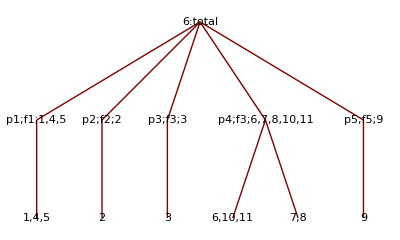

initial

the variables to record  the values of three kinds decomposition.

```mathematica
Once[quarkflow`qfb`quench=Table[0,{if,1,7,1},{io,1,8,1}]];
```

```mathematica
Once[quarkflow`qfa`sea=Table[0,{if,1,7,1},{io,1,8,1}]];
```

```mathematica
Once[quarkflow`qfa`valence=Table[0,{if,1,7,1},{io,1,8,1}]];
```

## quarkflow`channel

the variables to record  the channels of three kinds decomposition.

```mathematica
Once[quarkflow`qfb`quench`channel=Table[0,{if,1,7,1},{io,1,8,1}]];
```

```mathematica
Once[quarkflow`qfa`sea`channel=Table[0,{if,1,7,1},{io,1,8,1}]];
```

```mathematica
Once[quarkflow`qfa`valence`channel=Table[0,{if,1,7,1},{io,1,8,1}]];
```

## dsafsd

this line is from  the  previous edition, in order to change text to number in the circulation.

```mathematica
quark`flavor={"u","d","s"};
```

```mathematica
quarkflow`decompose`symbolic//Dimensions
quarkflow`names//Dimensions
chqftransfer2//Dimensions
```

## order

1;1,4,5
2;2
3;3
4;6,10,11
5;7,
6;8,
7;9

fun`quarkflow`select

here consider the  quarks in different position of  quarkflow diagram

so the  EM vertex employed in calculation, i.e. in vertex generating nb, only gives the individual contributions of individual quark.

```mathematica
fun`quarkflow`select[qfa_,quarkflow`names_,quark_,sector_,position_]:=Select[(*quark sea loop select function gather by both "qfa" and "uubar" *)
Replace[quarkflow`names,(*pick qfb only*)
x_/;(StringContainsQ[ToString[x],qfa])->Nothing,1],(*pick qfa only*)
(SameQ[StringTake[StringExtract[ToString[#],"`"->sector],{position}],quark]&)(* pick according to the loop quark *)
]
```

fun`quarkflow`select gives a list which satisfy the u/d/s/quench/sea/valence request

qfb quench (all valence)

classified according to the EM coupling, on mesons or baryons

fun`quarkflow`select[qfa_(to remove),quarkflow`names_,quark_,sector_,position_]

remove "qfa"

```mathematica
Block[{tea,teb,tec},
Table[
(
quarkflow`qfb`quench⟦if,io⟧={
(
tea=fun`quarkflow`select["qfa",quarkflow`names⟦if,io⟧,quark`flavor⟦1⟧,1,1]
)/.quarkflow`decompose`symbolic⟦if,io⟧,(*u flavor*)

(
teb=fun`quarkflow`select["qfa",quarkflow`names⟦if,io⟧,quark`flavor⟦2⟧,1,1]
)/.quarkflow`decompose`symbolic⟦if,io⟧,(*d flavor*)

(
tec=fun`quarkflow`select["qfa",quarkflow`names⟦if,io⟧,quark`flavor⟦3⟧,1,1]
)/.quarkflow`decompose`symbolic⟦if,io⟧(*s flavor*)

}
);
quarkflow`qfb`quench`channel⟦if,io⟧={
tea,teb,tec
}/.chqftransfer2⟦if,io⟧;

,{if,1,7,1}
,{io,1,8,1}
];
];
```

quarkflow`qfa`sea

remove "qfb"

```mathematica
Block[{tea,teb,tec},
Table[

quarkflow`qfa`sea⟦if,io⟧={
(
tea=fun`quarkflow`select["qfb",
Select[
quarkflow`names⟦if,io⟧,
Or[
StringContainsQ[ToString[#],"p2"],
StringContainsQ[ToString[#],"p3"]
]&
],
quark`flavor⟦1⟧,1,1]
)/.quarkflow`decompose`symbolic⟦if,io⟧,(*u flavor*)

(
teb=fun`quarkflow`select["qfb",
Select[
quarkflow`names⟦if,io⟧,
Or[
StringContainsQ[ToString[#],"p2"],
StringContainsQ[ToString[#],"p3"]
]&
],
quark`flavor⟦2⟧,1,1]
)/.quarkflow`decompose`symbolic⟦if,io⟧,(*u flavor*)

(
tec=fun`quarkflow`select["qfb",
Select[
quarkflow`names⟦if,io⟧,
Or[
StringContainsQ[ToString[#],"p2"],
StringContainsQ[ToString[#],"p3"]
]&
],
quark`flavor⟦3⟧,1,1]
)/.quarkflow`decompose`symbolic⟦if,io⟧(*u flavor*)

};
(*give the strong interaction coefficients*)

quarkflow`qfa`sea`channel⟦if,io⟧={tea,teb,tec}/.chqftransfer2⟦if,io⟧;
(*give the correspond chpt channel *)

,{if,1,7,1}
,{io,1,8,1}
];
];
```

quarkflow`qfa`valence

remove "qfb"

```mathematica
Block[{tea,teb,tec},
Table[

quarkflow`qfa`valence⟦if,io⟧={
(
tea=fun`quarkflow`select["qfb",
Select[
quarkflow`names⟦if,io⟧,
Or[
StringContainsQ[ToString[#],"p1"],
StringContainsQ[ToString[#],"p4"],
StringContainsQ[ToString[#],"p5"]
]&
],
quark`flavor⟦1⟧,1,1]
)/.quarkflow`decompose`symbolic⟦if,io⟧,(*u flavor*)

(
teb=fun`quarkflow`select["qfb",
Select[
quarkflow`names⟦if,io⟧,
Or[
StringContainsQ[ToString[#],"p1"],
StringContainsQ[ToString[#],"p4"],
StringContainsQ[ToString[#],"p5"]
]&
],
quark`flavor⟦2⟧,1,1]
)/.quarkflow`decompose`symbolic⟦if,io⟧,(*u flavor*)

(
tec=fun`quarkflow`select["qfb",
Select[
quarkflow`names⟦if,io⟧,
Or[
StringContainsQ[ToString[#],"p1"],
StringContainsQ[ToString[#],"p4"],
StringContainsQ[ToString[#],"p5"]
]&
],
quark`flavor⟦3⟧,1,1]
)/.quarkflow`decompose`symbolic⟦if,io⟧(*u flavor*)

};
(*give the strong interaction coefficients*)

quarkflow`qfa`valence`channel⟦if,io⟧={tea,teb,tec}/.chqftransfer2⟦if,io⟧;
(*give the correspond chpt channel *)

,{if,1,7,1}
,{io,1,8,1}
];
];
```

```mathematica
quarkflow`qfa`valence`channel//Dimensions
```

## storage

name`quarkflow

```mathematica
name`quarkflow`qfb`quench=FileNameJoin[{Directory[],"quarkflow.qfb.quench.m"}];
name`quarkflow`qfa`sea=FileNameJoin[{Directory[],"quarkflow.qfa.sea.m"}];
name`quarkflow`qfa`valence=FileNameJoin[{Directory[],"quarkflow.qfa.valence.m"}];
```

```mathematica
name`quarkflow`qfa`valence`channel=FileNameJoin[{Directory[],"quarkflow.qfa.valence.channel.m"}];
name`quarkflow`qfa`sea`channel=FileNameJoin[{Directory[],"quarkflow.qfa.sea.channel.m"}];
name`quarkflow`qfb`quench`channel=FileNameJoin[{Directory[],"quarkflow.qfb.quench.channel.m"}];
```

## decompose

```mathematica
name`quarkflow`names=FileNameJoin[{Directory[],"quarkflow.names.m"}];
```

```mathematica
name`quarkflow`decompose`symbolic=FileNameJoin[{Directory[],"quarkflow.decompose.symbolic.m"}];
```

```mathematica
name`chptquark`transfereq=FileNameJoin[{Directory[],"chptquark-transfereq.m"}];
name`chqftransfer1=FileNameJoin[{Directory[],"chpt-to-quarkflow.m"}];
name`chqftransfer2=FileNameJoin[{Directory[],"quarkflow-to-chpt.m"}];
```

quench-sea-valence

```mathematica
Put[
quarkflow`qfb`quench,
name`quarkflow`qfb`quench
];
Put[
quarkflow`qfa`sea,
name`quarkflow`qfa`sea
];
Put[
quarkflow`qfa`valence,
name`quarkflow`qfa`valence
];
```

quench-sea-valence  channel

```mathematica
Put[
quarkflow`qfa`valence`channel,
name`quarkflow`qfa`valence`channel
];
Put[
quarkflow`qfa`sea`channel,
name`quarkflow`qfa`sea`channel
];
Put[
quarkflow`qfb`quench`channel,
name`quarkflow`qfb`quench`channel
];
```

decompose

```mathematica
Put[
quarkflow`decompose`symbolic,
name`quarkflow`decompose`symbolic
];
```

chpt-quark relation

```mathematica
Put[
chptquark`transfereq,
name`chptquark`transfereq
];
```

```mathematica
Put[
chqftransfer1,
name`chqftransfer1
];
Put[
chqftransfer2,
name`chqftransfer2
];
```

```mathematica
Put[
quarkflow`names,
name`quarkflow`names
];
```